```mathematica
generateColors[n_]:=Table[Hue[Round[i/(2*n),.01/2],.8,.8],{i,n}];
```

```mathematica
folder="C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Analytic_Volume_10_TimeSize_5";files=FileNames["*.csv",folder];
analyticData=Association[Table[file = Import[f]; file[[1,1]]->file[[;;,2]],{f,files}]];
```

```mathematica
sortedAssociationData=SortBy[analyticData,Mean];
```

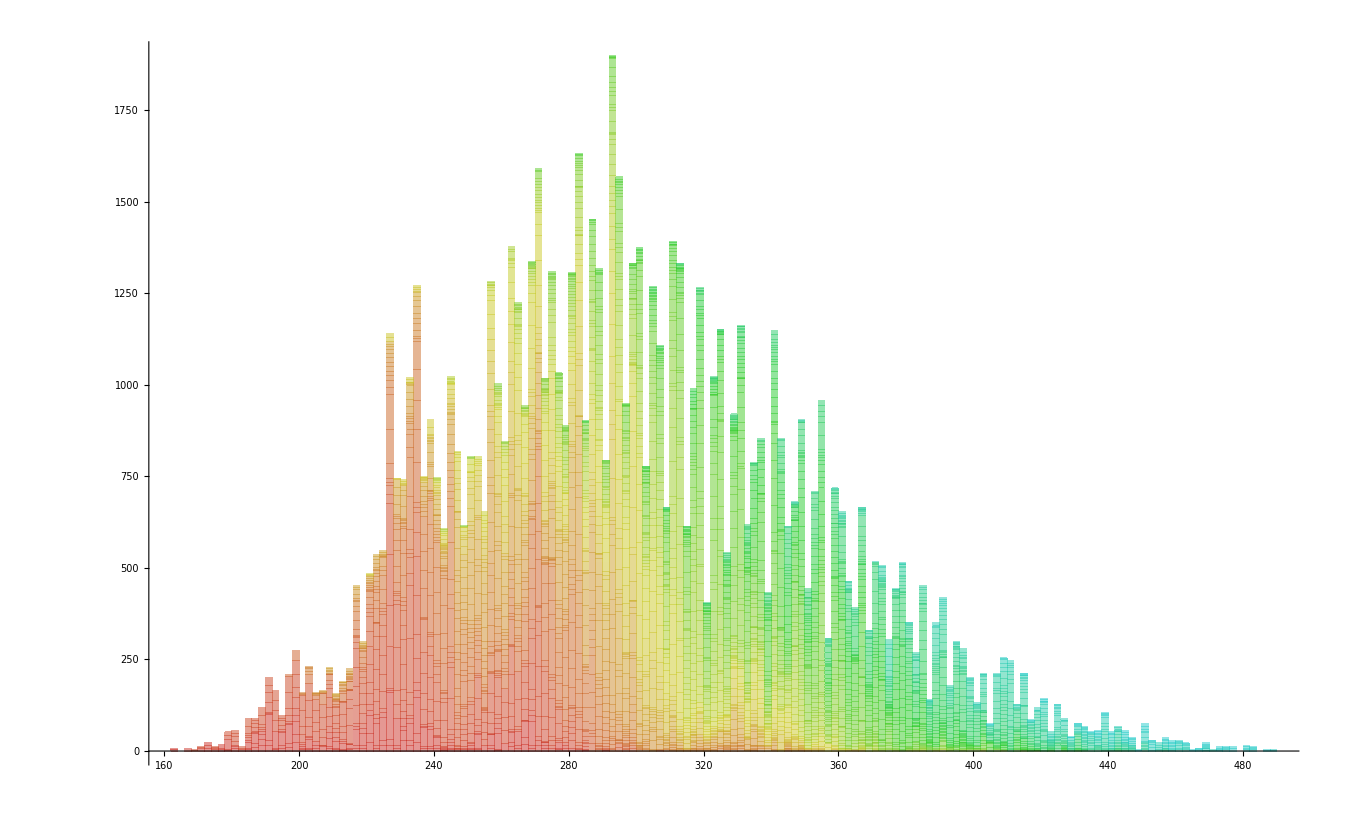

```mathematica
sortedData =SortBy[Values[analyticData],Mean];
Histogram[sortedData,100,ChartStyle->generateColors[Length[sortedData]],ChartLayout->"Stacked",ChartBaseStyle->EdgeForm[None]]
```

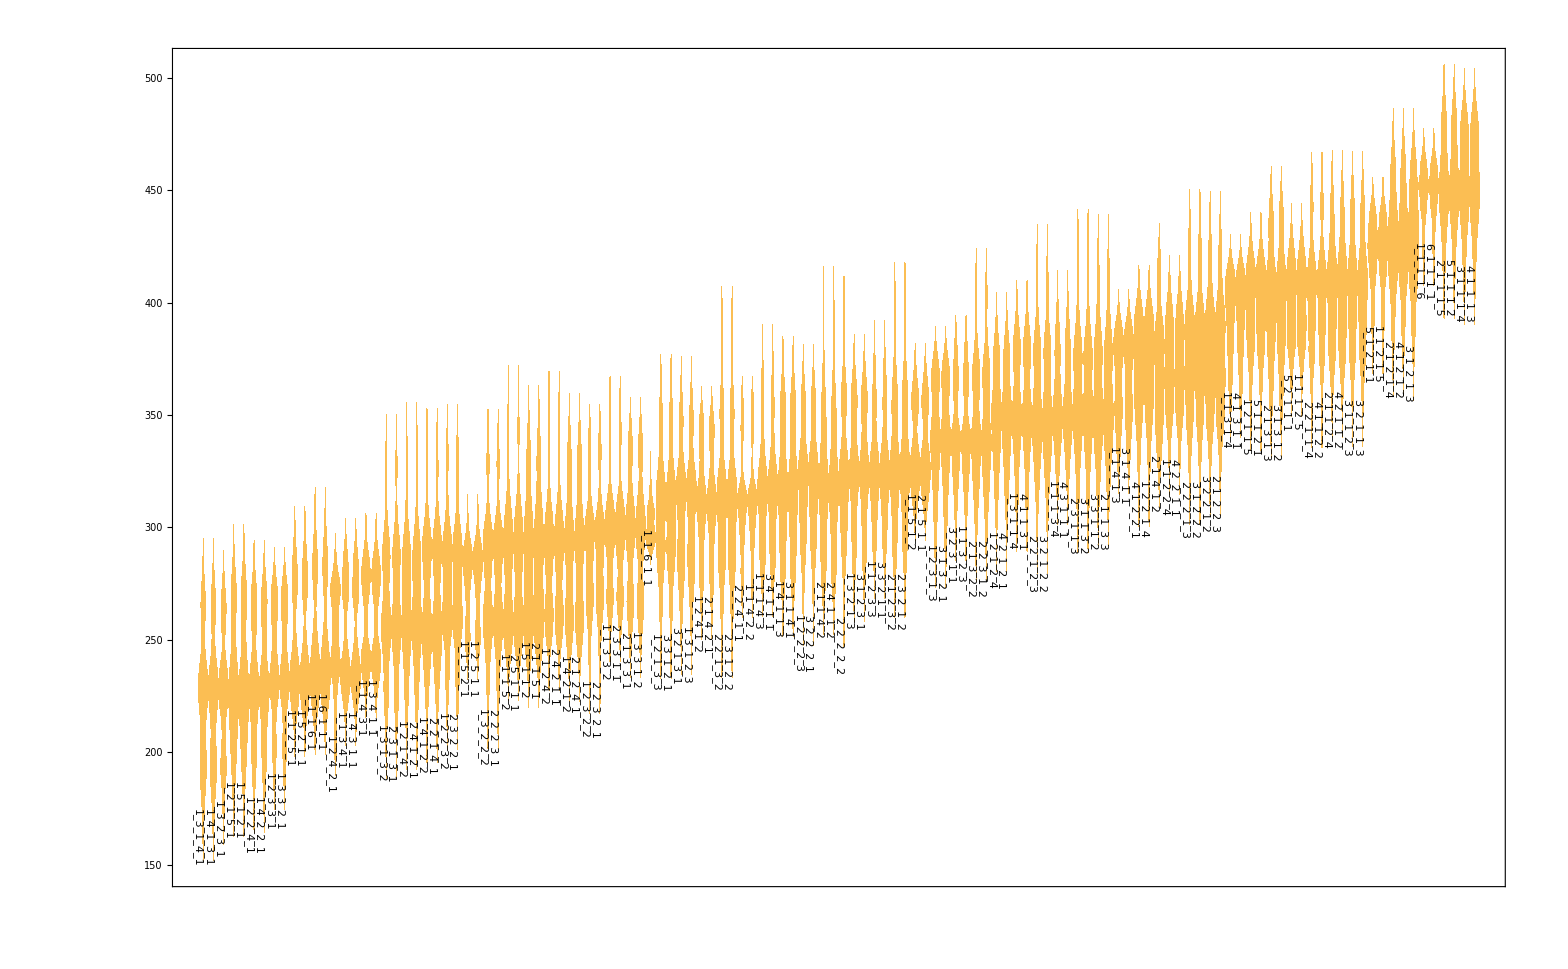

```mathematica
DistributionChart[sortedAssociationData,ChartStyle->{EdgeForm[None](*,"Pastel"*)},ChartLabels->Placed[Automatic,Below,Rotate[#,-Pi/2]&],ChartElementFunction->"SmoothDensity"]
```